The first task in making Polypool is setting up a bunch of data. In this cell, we create a polygon, get its boundary and centroid, and then pick a random point on the boundary to “start off”. The variable initial direction represents the “ray” that was created by moving from the center of the polygon to the boundary. It’s used later to start the raycast chain reaction.

```mathematica
n = RandomInteger[{3,6}];
poly = RandomPolygon[{"Convex",n}];
boundary = RegionBoundary[poly];
centroid = RegionCentroid[poly];
breakPoint = RandomPoint @ boundary;
initialDirection = breakPoint - centroid;
```

### Utility Functions

The following cells are all basic utility functions that are used in the main raycasting algorithm. These are used to simplify the actual text of the main algorithm, and do basic geometric conversions on points and lines.

First off we have sideList, which has a pretty self explanatory name. sideList simply takes a polygon and finds the list of Line objects that make up the edges of that polygon. This is distinct from the boundary of a polygon, which is one big Line object that can be cumbersome to use (sideList is even implemented using RegionBoundary). Both sideList and the RegionBoundary function that I used above serve similar purposes but create different representations of the same to make it easier to use that information later on.

```mathematica
sideList[poly_] := Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ RegionBoundary[poly]));
```

getCurrentSide is named in a pretty self-explanatory way (or at least I’d hope). Given a point in a polygon, getCurrentSide returns (hopefully) the edge of the polygon that the point is on. The only edge case in which this doesn’t work is when a point is exactly on a vertex or when the point isn’t on any vertex, though only the first scenario is possible in this simulation.

```mathematica
getCurrentSide[poly_,point_] := Extract[#,{1}]& @ First @ SortBy[RegionDistance[#,point]&] @ sideList[poly];
```

This function is a little strange. In Wolfram Language, we represent a line sensibly as a list of two points. However, for directional calculations, we need a line to represented differently. What this function does is change a line from a list of points to a horizontal and vertical distance that can be oriented anywhere.

```mathematica
lineToVecRep[line_] := (
line[[2]]-line[[1]]
);
```

### The Main Algorithm

This section discusses the “main algorithm” that I’ve been referring to in the previous sections of this essay. It is implemented in one function, castRayPolygon and castRayPolygonNestable. These functions take an abstract representation of a ray and figure out where it will collide with the polygon again. This can be naively iterated over to compute many raycasts, though it is very slow and violates many Wolfram Language best practices, so castRayPolygon allows the algorithm to be executed in accordance with the functional paradigm.

#### castRayPolgon

In the interest of being thorough, I’ll walk through castRayPolygon step-by-step. First and foremost, the function takes two parameters. The parameter point represents the intersection of the previous ray and the polygon, while originVector represents that ray in vector form. We take advantage of sideList from earlier to get access to each side of the polygon, and then find which side of the polygon the ray has intersected. We then use calculateNewDirection to create a ray originating from our original point parameter in our new direction. Once we have an actual ray object, we can calculate an intersection point and then return. The distinction between possibleCollisions and pointOfCollision is that RegionIntersection could possibly include the base of the ray, which would mess up the outputs.

```mathematica
castRayPolygon[poly_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,pointOfCollision,oppRay,newDirection,possibleCollisions},
sides = sideList[poly];
currentSide = getCurrentSide[poly,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
possibleCollisions =   (List @@ RegionIntersection[ray,RegionBoundary@ poly])[[1]];
pointOfCollision = Last @ (SortBy[EuclideanDistance[#,point]&][possibleCollisions]);
{pointOfCollision, point,newDirection}
];
```

#### castRayPolygonNestable

You can see that castRayPolygonNestable is tiny compared to its namesake.

```mathematica
castRayPolygonNestable[poly_, {point_,originVector_}] := (
	castRayPolygon[poly,point,originVector][[{1,3}]]
);
```

This function calculates the new direction vector of the ball based on the incoming direction and the side that it hit.  In a collision, the incoming angle of the ball and the outgoing angle of the ball have to be equal, just mirrored. This function accomplishes that with some basic linear algebra. In the raycasting algorithm, getting the new direction of the ray is the second major component. I’d also like to credit my good friend Christopher Gilbert for coming up with this vector equation.

```mathematica
calculateNewDirection[originVector_, sideVec_]:= (
Normalize[(2*Projection[originVector,sideVec]-originVector)]
);
```

```mathematica
rays = {};
AppendTo[rays, Line[{breakPoint,centroid}]];
```

```mathematica
castInfo = castRayPolygon[poly, breakPoint, breakPoint-centroid];
AppendTo[rays,Line[{castInfo[[2]],castInfo[[1]]}]];
```

```mathematica
casts = Reap @ Nest[Sow[castRayPolygonNestable[poly,#]]&,{breakPoint,breakPoint-centroid},10];
AppendTo[rays, Line /@ Partition[(Transpose @ casts[[2]][[1]] )[[1]],2,1]];
```

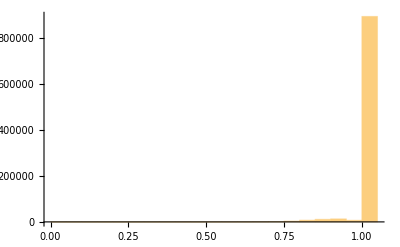

```mathematica
rayPainting = Graphics[{Opacity[0.05],rays}];
Histogram[DeleteElements[#,Range[0.9,1,0.001]]& @ Flatten @ ImageData @ Rasterize@rayPainting ]
```

```mathematica
ImageHistogram [ ColorConvert[Rasterize[rayPainting],"Grayscale"]]
```

## Works Cited

https://mathematica.stackexchange.com/questions/26770/getting-rgba-data-from-an-image
https://paulbourke.net/geometry/pointlineplane/